```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ujwalkumar/Desktop/Classes/Semester 8/Computational Physics/Homework 7

```mathematica
data=ReadList["!./ratio 3 .1 2 .1 100000",Number];
```

ratio(mean,err): {3/2,0.0901388}

UniformDistribution::lss: Parameter 3/2 at position {1,1} in UniformDistribution[{3/2,0.0901388}] is expected to be less than 0.0901388.

UniformDistribution::lss: Parameter 1.5 at position {1,1} in UniformDistribution[{1.5,0.0901388}] is expected to be less than 0.0901388.

General::stop: Further output of UniformDistribution::lss will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,PlotLabel→,Null].

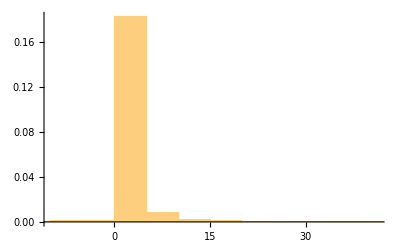
Show[-Graphics-,-Graphics-,PlotLabel→,Null]

```mathematica
mx=3;sx=0.1;
my=2;sy=0.1;
mr=mx/my;sr=√(sx^2/my^2+sy^2 mx^2/my^4);
Print["ratio(mean,err): ",{mr,sr}];
Show[Histogram[data,10000,"PDF"],Plot[PDF[UniformDistribution[{mr,sr}]][x],{x,-4,4},PlotRange->All], PlotLabel-> "", ]
```

```mathematica
data=ReadList["!./ratio 3 1 2 1 100000",Number];
```

ratio(mean,err): {1.5,0.901388}

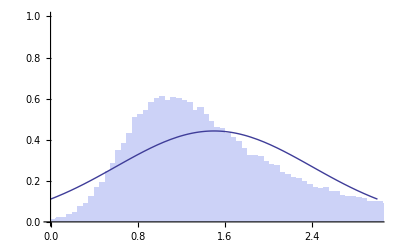

```mathematica
mx=3;sx=1.;
my=2.;sy=1.;
mr=mx/my;sr=√(sx^2/my^2+sy^2 mx^2/my^4);
Print["ratio(mean,err): ",{mr,sr}];
Show[Histogram[data,{0,5,5/100},"PDF",PlotRange->{{0,3},{0,1}}],Plot[PDF[NormalDistribution[mr,sr]][x],{x,0,3},PlotRange->All]]
```

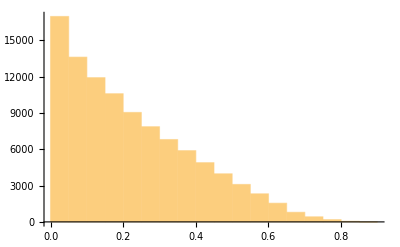

Mean of the variance computed over all trials: 0.222474

```mathematica
Block[{n=3,ntrials=100000,data,res},
data=Partition[RandomVariate[UniformDistribution[{0,2}],n*ntrials],3];
res=Table[m=Mean[l];Total[(l-m)^2]/(n),{l,data}];
Print@Histogram[res];
Print["Mean of the variance computed over all trials: ",Mean[res]]
]
```